```mathematica
{ru, init, txspec} = {{299459058088077823758143088095350287424,4,1}, {{1}, 0},{200, {-110, 110}}};
```

### Width history prediction

#### Getting training data

```mathematica
awh = Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0},txspec =  {200, {-110, 110}}, aps, pca, ca},(If[# == {}, 0,  #[[2]] - #[[1]] +1]&[nonzeroRange[#]]&/@ PerturbedCellularAutomaton[ru, init, txspec, #, "ReturnPerturbations"->False]&/@ allperts[ru, init, txspec])];
```

```mathematica
rh = Module[
{ru = {299459058088077823758143088095350287424,4,1},
init = {{1}, 0},txspec =  {200, {-110, 110}}, aps, pca, ca},
SeedRandom[444666];
HealCA[ru, init, txspec, #, 1, (# == 101&)]&/@ RandomSample[allperts[ru, init, txspec],10]];
```

$Aborted

```mathematica
rh
```

{{<|{63,116}→2|>},{<|{41,125}→1|>},{<|{89,113}→2|>},{},{<|{89,108}→3|>},{<|{28,113}→1|>},{<|{73,115}→2|>},{<|{82,129}→2|>},{},{<|{59,124}→1|>}}

```mathematica
rh = Module[
{ru = {299459058088077823758143088095350287424,4,1},
init = {{1}, 0},txspec =  {200, {-110, 110}}, aps, pca, ca},
SeedRandom[444666];
ParallelMap[HealCA[ru, init, txspec, #, 1, (80<# < 120&), "Order"->"Random"]&,Select[allperts[ru, init, txspec], 30<Keys[#][[1, 1]]<60&]]];
```

```mathematica
alltrain =Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0},txspec =  {200, {-110, 110}}, aps, pca, ca},
MapThread[If[# == {}, 0,  #[[2]] - #[[1]] +1]&[nonzeroRange[#]]&/@ PerturbedCellularAutomaton[ru, init, txspec, #1, "ReturnPerturbations"->False]->Keys[#2][[1, 1]]&, {Select[allperts[ru, init, txspec], 30<Keys[#][[1, 1]]<60&], Catenate[rh]}]];
```

How good are these healers anyway?

```mathematica
nr =Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0},txspec =  {200, {-110, 110}}, aps, pca, ca},
MapThread[TestCALifeTime[PerturbedCellularAutomaton[ru, init, txspec,Join[#1, #2], "ReturnPerturbations"->False]]&, {Select[allperts[ru, init, txspec], 30<Keys[#][[1, 1]]<60&], Catenate[rh]}]];
```

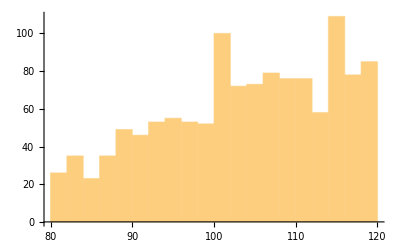

```mathematica
Histogram[nr]
```

Answer: pretty good

```mathematica
Length[alltrain]
```

1233

#### Training

```mathematica
SeedRandom[222444];
test = alltrain[[ti = RandomSample[Range[Length[Select[allperts[ru, init, txspec], 30<Keys[#][[1, 1]]<60&]]], 223]]];
```

```mathematica
train = Delete[alltrain, List/@ti];
```

```mathematica
p = Predict[train]
```

PredictorFunction[…]

#### Testing

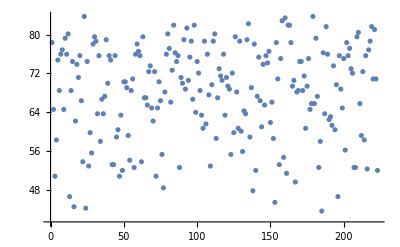

```mathematica
ListPlot[(p/@ test[[All, 1]]), PlotHighlighting->None]
```

Loss:

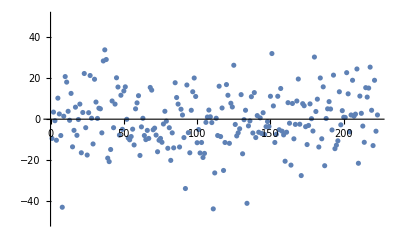

```mathematica
ListPlot[test[[All, 2]] - (p/@ test[[All, 1]]), PlotHighlighting->None, PlotRange->{-50, 50}]
```

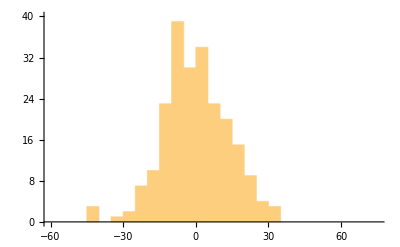

```mathematica
Histogram[test[[All, 2]] - (p/@ test[[All, 1]]), {5}, PlotRange->{{-60, 75},{0, 40} }]
```

Random guess for comparison:

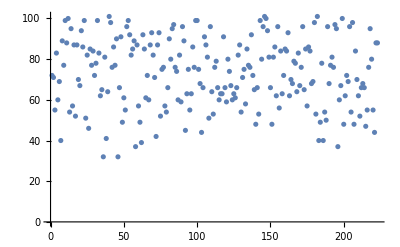

```mathematica
SeedRandom[444555];ListPlot[RandomInteger[{Keys[#][[1, 1]], 101}]&/@ Select[allperts[ru, init, txspec], 30<Keys[#][[1, 1]]<60&][[ti]], PlotHighlighting->None]
```

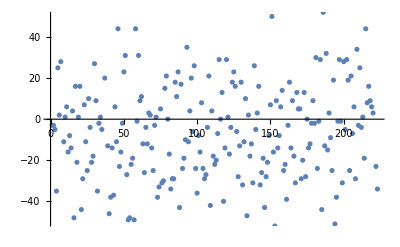

```mathematica
SeedRandom[444555];
With[{aps = Select[allperts[ru, init, txspec], 30<Keys[#][[1, 1]]<60&]}, ListPlot[test[[All, 2]] -( RandomInteger[{Keys[aps[[#]]][[1, 1]], 101}]&/@ ti), PlotHighlighting->None, PlotRange->{-50, 50}]]
```

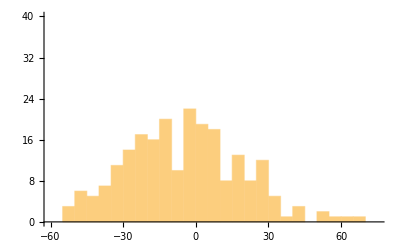

```mathematica
SeedRandom[444555];
Histogram[test[[All, 2]] - (RandomInteger[{Keys[#][[1, 1]], 101}]&/@ Select[allperts[ru, init, txspec], 30<Keys[#][[1, 1]]<60&][[ti]]), {5}, PlotRange->{{-60, 75},{0, 40} }]
```

#### Viz with growth curve

```mathematica
cawh = Counts[awh];
```

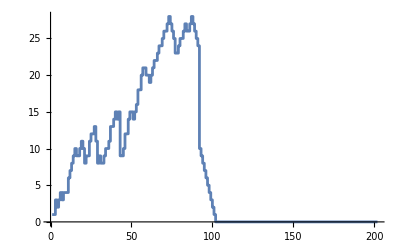
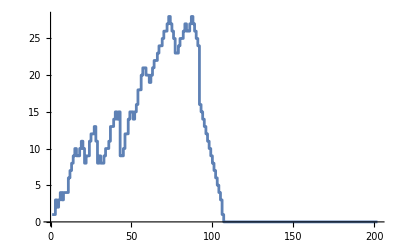
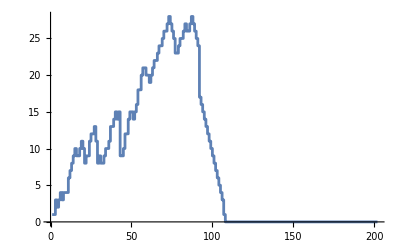
{-Graphics-224,-Graphics-80,-Graphics-66}

```mathematica
KeyValueMap[Labeled[ListStepPlot[#1], Text[#2]]&, Take[ReverseSort[cawh], 3]]
```

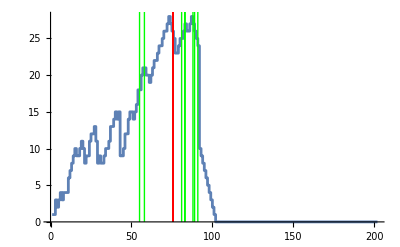
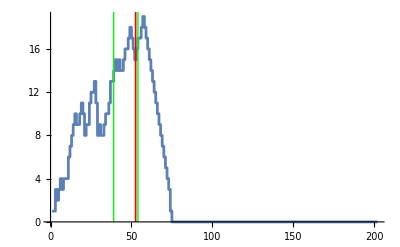
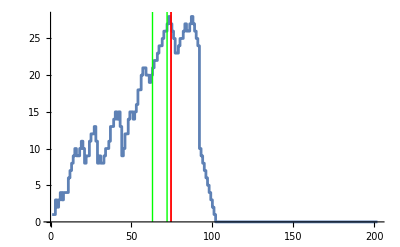
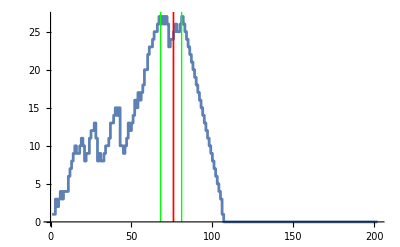
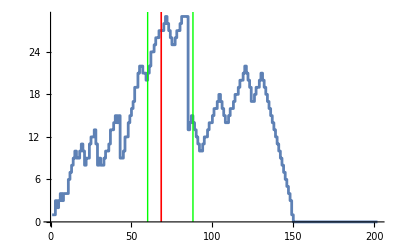
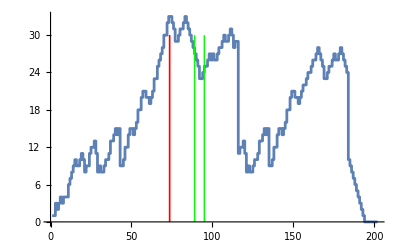
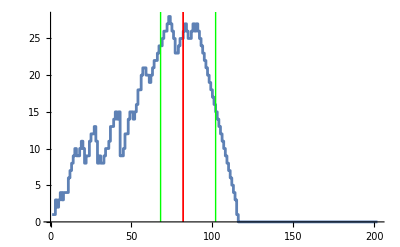
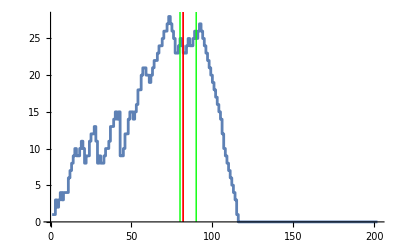
{-Graphics-9,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1}

```mathematica
With[{aps = Select[allperts[ru, init, txspec], 30<Keys[#][[1, 1]]<60&], res = p/@alltrain[[All, 1]]},KeyValueMap[Labeled[Show@@{ListStepPlot[#1, PlotHighlighting->None], 
Graphics[
Join[{Green},
Line[{{Keys[First[rh[[#]]]][[1, 1]], 0},{Keys[First[rh[[#]]]][[1, 1]], 30}}]& /@ #2,
{Red},
Line[{{res[[#]], 0},{res[[#]], 30}}]& /@ #2]
]}, Text[Length[#2]]]&,
ReverseSortBy[GroupBy[ti, (If[# == {}, 0,  #[[2]] - #[[1]] +1]&[nonzeroRange[#]]&/@ PerturbedCellularAutomaton[ru, init, txspec, aps[[#]], "ReturnPerturbations"->False]& )], Length]][[;;20]]]
```

### Evolution history for main rule

```mathematica
<|"Element"->{{{268421576596783154125046530204266236812,4,1},111},{{147403944448280291853900806387327553596,4,1},107},{{248165598297832837437916710957193630216,4,1},104},{{134352701883209903342527245958435650060,4,1},102},{{288096107223535296419424673988897412364,4,1},106},{{339118334212898847537752633217327057976,4,1},109},{{321033973632549904983932956520209330696,4,1},101},{{105095753086267005525767099158674078604,4,1},106},{{267017653732987573795364345207890141512,4,1},103},{{110572144621941770841649306920052872204,4,1},104},{{285844326421166081060892845611091535884,4,1},111},{{76459985983155900365494599730072701452,4,1},101},{{287426194400923611234870030427559824140,4,1},103},{{328091281327807596318497304928484883976,4,1},102},{{119036002119603607356514909757868286216,4,1},102},{{317299368495465910304892902399080254264,4,1},107},{{278045845346607563032787258414437791544,4,1},101},{{117583592864712737061416347667069988156,4,1},101},{{4805101858768707264031667489079952184,4,1},108},{{7977385475371059556823827836905458188,4,1},102},{{28822720352419846592599677408367493436,4,1},101},{{46058842733434566198293092266537120384,4,1},101},{{299459058088077823758143088095350287424,4,1},101},{{140760482982177850157208130958283113584,4,1},104},{{68344969204256202378277879430275436104,4,1},102},{{25359040487030105047738027699989445448,4,1},124},{{50384664521204969494536571058688395144,4,1},101},{{275829246158421973968735855928619872784,4,1},104},{{187801454374097774235135078616998547980,4,1},102},{{94341792732834871885391301103528730764,4,1},118},{{123547048548354375987206496656127777288,4,1},104},{{145847175969039188329249499360869168136,4,1},101},{{50742575811329985903162916962404076296,4,1},112},{{17236508088123058982014956771682294592,4,1},103},{{44467251686122792070513828103482331660,4,1},105},{{179559826355654686003966918665743860592,4,1},107},{{66958958108797332090631032629696739612,4,1},109}},"Index"->{17,29,240,264,352,417,444,885,1123,1214,1537,1666,1679,1726,2423,2445,2505,2525,2529,2578,2737,2774,2845,3212,3497,3624,3800,3830,3925,4038,4060,4143,4668,4714,4838,4896,4906}|>;
```